```mathematica
ClearAll;
(*Here I'm setting up the shrodinger equation.*)
eqn= D[ψ[x],{x,2}]==-k^2 ψ[x];
(*Let's use Dsolve to get our solutions*)
sol =DSolve[eqn,ψ[x],{x}]/. k-> √((2m E)/h)
```

{{ψ[x]→C[1] Cos[√(2 ⅇ) √(m/h) x]+C[2] Sin[√(2 ⅇ) √(m/h) x]}}

The general solution to our problem is ψ[x] = Aⅇ^(ik x)+Bⅇ^(-ik x) .
ψ[-l/2] = ψ[l/2] = 0.
(1) ψ[-l/2] = Aⅇ^(ik (-l/2))+Bⅇ^(-ik(-l/2))
(2) ψ[l/2] = Aⅇ^(ik (l/2))+Bⅇ^(-ik(l/2))
From the first equation B = -ⅇ^-iklA
Plug this into the second equation, then:
Aⅇ^(ik (-l/2))-Aⅇ^(-ik(3l/2))=0  → Aⅇ^(ik (l/2))(1-ⅇ^(-2ikl))=0
In order for this function to be zero, either A and B are zero, meaning there is no wave function, or ⅇ^(-2ikl) = 1. This latter condition implies that 2ikl = 2inπ, where n is an integer. We get that k=nπ/l, and B=−ⅇ^-inπA. In the cases where n is even, we have B = −A.
A(ⅇ^ikx-ⅇ^-ikx)=ψ[x]=2Asin(kx)
or in the cases when n is odd we have B = Af
A(ⅇ^ikx+ⅇ^-ikx)=ψ[x]=2Acos(kx)
So in the cases where the the potential is symmetric we can use cos, and when its antisymmetric we can use sin. Here since the potential is symmetric we can use cos instead of sin.
This means that ψ[x] =  Piecewise[{{Sqrt[2/l] Cos[n Pi x/l], n Odd}, {Sqrt[2/l] Sin[n Pi x/l], n Even}}]

(19.4233 | -1.45358 | 1.7359 | -1.18714 | 0.81029 | -0.578259 | 0.430675 | -0.332274 | 0.263775 | -0.214317 | 0.177499 | -0.149377 | 0.127424 | -0.109967 | 0.0958582
-1.45358 | 67.4323 | -1.01359 | 1.46793 | -1.01825 | 0.698646 | -0.501162 | 0.375419 | -0.291414 | 0.232756 | -0.190237 | 0.158444 | -0.134047 | 0.114913 | -0.0996255
1.7359 | -1.01359 | 148.275 | -0.844697 | 1.35628 | -0.941153 | 0.64339 | -0.460302 | 0.344399 | -0.267333 | 0.213701 | -0.174907 | 0.145933 | -0.123706 | 0.10627
-1.18714 | 1.46793 | -0.844697 | 261.719 | -0.767601 | 1.30103 | -0.900294 | 0.61237 | -0.436221 | 0.325344 | -0.252004 | 0.201189 | -0.164566 | 0.137289 | -0.116409
0.81029 | -1.01825 | 1.35628 | -0.767601 | 407.664 | -0.726741 | 1.27001 | -0.876213 | 0.593315 | -0.420892 | 0.312833 | -0.241663 | 0.192546 | -0.157269 | 0.131073
-0.578259 | 0.698646 | -0.941153 | 1.30103 | -0.726741 | 586.078 | -0.70266 | 1.25095 | -0.860883 | 0.580804 | -0.410551 | 0.304189 | -0.234365 | 0.18633 | -0.151931
0.430675 | -0.501162 | 0.64339 | -0.900294 | 1.27001 | -0.70266 | 796.948 | -0.687331 | 1.23844 | -0.850542 | 0.57216 | -0.403253 | 0.297973 | -0.229028 | 0.181713
-0.332274 | 0.375419 | -0.460302 | 0.61237 | -0.876213 | 1.25095 | -0.687331 | 1040.27 | -0.67699 | 1.2298 | -0.843245 | 0.565944 | -0.397916 | 0.293356 | -0.225007
0.263775 | -0.291414 | 0.344399 | -0.436221 | 0.593315 | -0.860883 | 1.23844 | -0.67699 | 1316.04 | -0.669692 | 1.22358 | -0.837907 | 0.561327 | -0.393895 | 0.289834
-0.214317 | 0.232756 | -0.267333 | 0.325344 | -0.420892 | 0.580804 | -0.850542 | 1.2298 | -0.669692 | 1624.25 | -0.664355 | 1.21896 | -0.833887 | 0.557805 | -0.390793
0.177499 | -0.190237 | 0.213701 | -0.252004 | 0.312833 | -0.410551 | 0.57216 | -0.843245 | 1.22358 | -0.664355 | 1964.92 | -0.660334 | 1.21544 | -0.830784 | 0.555058
-0.149377 | 0.158444 | -0.174907 | 0.201189 | -0.241663 | 0.304189 | -0.403253 | 0.565944 | -0.837907 | 1.21896 | -0.660334 | 2338.02 | -0.657232 | 1.21269 | -0.828341
0.127424 | -0.134047 | 0.145933 | -0.164566 | 0.192546 | -0.234365 | 0.297973 | -0.397916 | 0.561327 | -0.833887 | 1.21544 | -0.657232 | 2743.58 | -0.654788 | 1.21051
-0.109967 | 0.114913 | -0.123706 | 0.137289 | -0.157269 | 0.18633 | -0.229028 | 0.293356 | -0.393895 | 0.557805 | -0.830784 | 1.21269 | -0.654788 | 3181.57 | -0.652829
0.0958582 | -0.0996255 | 0.10627 | -0.116409 | 0.131073 | -0.151931 | 0.181713 | -0.225007 | 0.289834 | -0.390793 | 0.555058 | -0.828341 | 1.21051 | -0.652829 | 3652.02)

{{19.3491,67.4462,148.295,261.731,407.671,586.082,796.951,1040.27,1316.04,1624.26,1964.92,2338.03,2743.58,3181.58,3652.02},{{0.999458,0.0297293,-0.0131606,0.00465483,-0.00194772,0.000946255,-0.000513247,0.000302043,-0.000189184,0.000124462,-0.0000852027,0.0000602737,-0.0000438323,0.0000326359,-0.0000247941},{-0.0295143,0.999445,0.0130116,-0.00764949,0.00298532,-0.00132973,0.000675567,-0.000379416,0.000229764,-0.000147442,0.00009905,-0.000069057,0.0000496472,-0.0000366275,0.0000276196},{-0.013489,0.0125393,-0.999784,-0.00767586,0.00528284,-0.00215152,0.000985452,-0.000511327,0.00029223,-0.000179677,0.000116877,-0.0000794877,0.0000560431,-0.0000407075,0.0000303111},{-0.00496534,0.00758073,-0.00747543,0.999907,0.00536697,-0.00403716,0.00168137,-0.000781653,0.00041024,-0.000236739,0.000146832,-0.0000962858,0.0000659821,-0.0000468551,0.0000342574},{0.00212603,-0.00302419,0.00524445,-0.00527085,0.99995,0.00413042,-0.00327617,0.00138331,-0.000649106,0.000343114,-0.000199204,0.000124234,-0.0000818914,0.0000563992,-0.0000402352},{0.00103971,-0.00136716,0.00216791,-0.00401904,0.0040757,-0.999969,-0.00336629,0.00276227,-0.00117737,0.000556099,-0.000295421,0.000172235,-0.000107825,0.0000713329,-0.0000492898},{-0.000563388,0.000697654,-0.00100429,0.00169332,-0.00326653,0.00333103,-0.999979,-0.00284711,0.0023909,-0.00102621,0.000487115,-0.000259756,0.000151922,-0.0000953803,0.0000632574},{-0.000330357,0.000391473,-0.000522974,0.000794833,-0.00139258,0.00275647,-0.00282238,0.999985,0.00247058,-0.00210937,0.000910301,-0.000433812,0.000232041,-0.00013606,0.0000855987},{-0.000206061,0.000236389,-0.000298684,0.000418563,-0.000659035,0.00118467,-0.00238706,0.0024522,-0.999988,-0.00218441,0.00188824,-0.000818455,0.000391332,-0.000209864,0.000123296},{-0.000135036,0.00015119,-0.000183212,0.000241472,-0.000349492,0.000563832,-0.00103206,0.00210663,-0.00217018,0.999991,0.00195922,-0.00170978,0.000743822,-0.000356667,0.000191664},{0.0000921243,-0.000101248,0.000118844,-0.000149496,0.000202915,-0.000300462,0.000493292,-0.000915069,0.0018862,-0.00194786,0.999993,0.00177723,-0.00156267,0.000681985,-0.000327763},{0.0000649824,-0.0000703949,0.0000806103,-0.0000978128,0.000126378,-0.000175225,0.000263837,-0.000438861,0.000822421,-0.00170822,0.00176798,-0.999994,-0.00162722,0.00143944,-0.000629788},{-0.000047149,0.0000504962,-0.0000567065,0.0000668879,-0.0000831634,0.000109597,-0.000154392,0.00023543,-0.000395565,0.000747217,-0.00156153,0.00161967,-0.999995,-0.0015021,0.00133445},{-0.0000350554,0.0000372013,-0.0000411281,0.0000474289,-0.0000572003,0.0000724363,-0.0000969051,0.000138185,-0.000212796,0.000360374,-0.000685096,0.00143888,-0.00149641,0.999997,0.0013955},{0.0000266098,-0.0000280286,0.000030596,-0.0000346441,0.0000407704,-0.0000500154,0.0000642424,-0.0000869549,0.000125191,-0.000194301,0.000331162,-0.000632867,0.00133477,-0.00139224,0.999998}}}

Piecewise[{{19.3491, x≥0.78||x≤-0.78}, {19.3491+160.041 Cos[4.02768 x]+4.76049 Cos[8.05537 x]-2.10738 Cos[12.083 x]+0.745369 Cos[16.1107 x]-0.311885 Cos[20.1384 x]+0.151522 Cos[24.1661 x]-0.0821853 Cos[28.1938 x]+0.0483656 Cos[32.2215 x]-0.0302936 Cos[36.2491 x]+0.0199299 Cos[40.2768 x]-0.0136433 Cos[44.3045 x]+0.00965152 Cos[48.3322 x]-0.00701879 Cos[52.3599 x]+0.00522593 Cos[56.3876 x]-0.00397023 Cos[60.4152 x], True}}]

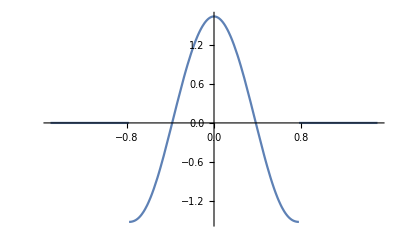

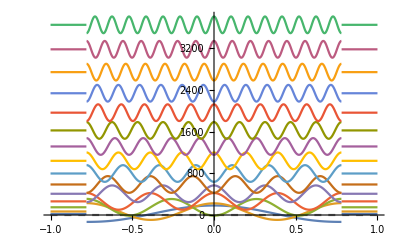

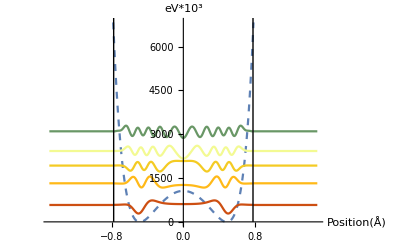

```mathematica
(* Okay, now that I've solved for the particle in a box, it's time to tackle the eigenvalue problem in equation 8. First I use a peicewise function to construct my basis functions, ensuring that the particle has boundaries at -l and l, and is always zero outside.*)
ClearAll;
pib[{n_Integer,l_},x_]:=Piecewise[{{0,x≤-l},{Sqrt[2/l] Cos[n Pi x/l],-l<x<l},{0,-l≤x≥l}}];
(*We can substitute this basis set with another one representing the HO, if it would represent our basis better*)
(*also, If we wanted to use the entire function, not just the cos form, we can use (1+(-1)^n) Sqrt[2/L] Sin[n Pi x/L]/2+(1-(-1)^n) Sqrt[2/L] Cos[n Pi x/L]/2, which eliminates the sin when odd and cos when even. But for some reason the solution doesn't look right when I use both the sin and cos functions*)
hel[{n_,m_,l_},pot_,{hb_,mu_},{min_,max_},x_]:=hel[{n,m,l},pot,{hb,mu},{min,max},x]=With[{psin=pib[{n,l},x],psim=pib[{m,l},x]},Quiet[NIntegrate[psin*(-hb/(2 mu) D[psim,{x,2}]+pot*psim),{x,min,max}],NIntegrate::ncvb]];
(*Here we get the elements of our hamiltonion by integrating over the two functions psim and psin. The counters are too keep track of the functions as we solve <Subscript[a, n]|Ĥ|Subscript[a, m]>. Here were just doing the inner product.*)
ham[nT_,l_,pot_,{hb_,mu_},{min_,max_},x_]:=Table[hel[{n,m,l},pot,{hb,mu},{min,max},x],{n,1,nT},{m,1,nT}];
(*Here we tabulate the results of our inner product over however many basis functions we want. our ham[] function will take the number of basis functions as a variable*)
(*Note that you can substitute in something else for PIB,like an HO wavefunction,if that will represent your basis better.The NIntegrate can be replaced by integrate if you're interested in analytical solutions. Now we can do some stuff to get the Hamiltonian for our specific system:*)
Enot=3;
Abar=3.2;
Xnot=0.5;
(*We can change any of our constants as we like. Here I've set them for this specific questions*)
V[x_]:=Enot*(1-Exp[-Abar(x+Xnot)])^2
W[x_]=V[x]+V[-x]-2.75543;
(*here is the potential well that we've set, we can change the values of a or E0 or X0 very easily from here.*)
$defaultLength=0.78;
$defaultHBar=1;
$defaultMass=1;
$defaultPot= W[x];
$defaultRange={-1.5,1.5};
(*Let's set up a series of default values for the well length, hbar, mass, and potential, here the default potential is our potential. We also set Hbar and the mass to equal one for simplicity's sake.*)
withDefaults[expr_]:=Block[{l=$defaultLength,b=$defaultBarrier,hb=$defaultHBar,m=$defaultMass,v=$defaultPot,r=$defaultRange},expr];
withDefaults~SetAttributes~HoldFirst;
(*let's make sure that our function uses the defaults given!*)
myHam[nT_]:=withDefaults[ham[nT,l,v,{hb,m},r,x]];
(*Here is the function that uses the defaults provided above and uses the PIB basis set to generate nT eigenfunctions*)
hamRep=myHam[15];
(*here are the 15 functions in our basis set in matrix form.*)
myHam[15]//MatrixForm
(* We've now used 15 basis functions of pib in matrix representation to construct the hamiltonian for our specific situation. Now we need to get out from the Hamiltonian our wavefunctions*)
getSolns[rep_]:=Module[{es=Eigensystem[rep],resorting,phasing},resorting=Ordering[es[[1]]];
phasing=Sign@es[[2,1]];
es=#[[resorting]]&/@es;
es]
(*A mathematica function that takes in our matrix representation and uses the function Eigensystem to give a list of the eigenvalues and eigenvectors of the square matrix [hamRep]*) 
solns=getSolns[hamRep]

expandSoln[vec_,l_,x_]:=Dot[vec,pib[{#,l},x]&/@Range[Length@vec]]
(*Dotting the given vectors with our pib basis set*)
shiftScaledWfns[es_,l_,x_]:=MapThread[#+100*expandSoln[#2,$defaultLength,x]&,es]
(*lets scale our wavefunctions so they're easier to see*)
solnWfs=shiftScaledWfns[solns,1,x];
solnWfs[[1]] //FullSimplify
(* Here we plot the first function in the eigenfunction solution set unscaled. The sum of basis set functions as peicewise functions in matrix rep can be shown below.*)
(*We have x plotted between -1.5 and 1.5 just to see what we've done for our first eigenfunction*)
Plot[Evaluate@expandSoln[solns[[2,1]],$defaultLength,x],{x,-1.5,1.5},PlotRange->All]
dubWell[shift_,scaling_]:=With[{base=W[x]&@shift},scaling*(base-(base/.x->(.5-shift)))];
Plot[Evaluate@Prepend[solnWfs,0],{x,-1,1},PlotStyle->Prepend[ColorData[97]/@Range[15],Directive[Dashed,Gray]]]
(*Here we can see all of our solved eigenfunctions plotted scaled up or else they would have some heavy overlap*)
V[x_]:=3.*(1-Exp[-3.2(x+0.5)])^2
W[x_]=V[x]+V[-x]-2.75543;
dubWell[shift_,scaling_]:=With[{base=W[x]&@shift},scaling*(base-(base/.x->(.5-shift)))];
dwp=dubWell[0,10^3];
(*this was already defined above, but here lets scale our functions so that they're easier to see*)
plotCustomSoln[pot_,basisSize:_Integer:6,plotSpec:{__Integer}|_Span: ;;3,ops:OptionsPattern[]]:=Block[{$defaultPot=pot,$defaultRange={-1.,1.}},Quiet@Plot[Evaluate@Prepend[shiftScaledWfns[getSolns[myHam[basisSize]],1,x][[plotSpec]],$defaultPot],{x,-1.5,1.5},ops,PlotStyle->Prepend[ColorData[35]/@Range[15],Directive[Dashed,Turqoise]]]]
(*lets finally get our solution. Here we set up the plot of the solution as a function of all the basis functions calculated above as well as the number of solutions we want to see*)
plotCustomSoln[dwp,15, ;;10;;2, AxesLabel->{"Position(Å)","eV*10^3"},Epilog->{Line[{{0.78,0},{0.78,10000000}}],Line[{{-0.78,0},{-0.78,10000000}}]}]
(* Here we've plotted the double well, the infinite well, and the first five numerically solved eigenfunctions to the eigenvalue problem*)
```

```mathematica
(*The particle in a box wavefunctions are very aggressively zero outside the l that we have set. This is extremely apparent in our final solution, where we can see that the probability once the wavefunction reaches past our walls are zero. A depends on the reciprocal length of the box. As A increases, L must become smaller and smaller. ynot is direcly linked to the ratio of xnot to L. This determines the location of the horizontal intercepts with relation to the edges of the well. Physically this means that as ynot increases and decreases, the well size and the double well potential shift to become bigger or smaller.*)
```

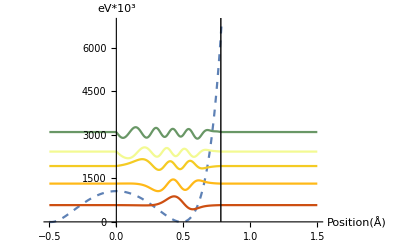

```mathematica
(*The reason why W[x] = W[-x] is so useful is that we can use the symmetry to solve for one side of the well and mirror it to the other side! I do the exact same thing here as I did above, but I only solve for a well from 0 to l, which uses sine as the basis functions. This solution shows that you can just find half of the solution for the well and just reflect it across to the other side, reducing calculation time.*)
ClearAll;
V[x_]:=3.*(1-Exp[-3.2(x+0.5)])^2
W[x_]=V[x]+V[-x]-2.75543;
pib[{n_Integer,l_},x_]:=Piecewise[{{0,x≤0},{Sqrt[2/l]*Sin[(n*Pi/l)*x],0<x<l},{0,x≥l}}];
hel[{n_,m_,l_},pot_,{hb_,mu_},{min_,max_},x_]:=hel[{n,m,l},pot,{hb,mu},{min,max},x]=With[{psin=pib[{n,l},x],psim=pib[{m,l},x]},Quiet[NIntegrate[psin*(-hb/(2 mu) D[psim,{x,2}]+pot*psim),{x,min,max}],NIntegrate::ncvb]];
ham[nT_,l_,pot_,{hb_,mu_},{min_,max_},x_]:=Table[hel[{n,m,l},pot,{hb,mu},{min,max},x],{n,1,nT},{m,1,nT}];
$defaultLength=.78;
$defaultHBar=1;
$defaultMass=1;
$defaultPot=W[x];
$defaultRange={-.5,1.5};

withDefaults[expr_]:=Block[{l=$defaultLength,b=$defaultBarrier,hb=$defaultHBar,m=$defaultMass,v=$defaultPot,r=$defaultRange},expr];
withDefaults~SetAttributes~HoldFirst;

myHam[nT_]:=withDefaults[ham[nT,l,v,{hb,m},r,x]];

hamRep=myHam[10];
getSolns[rep_]:=Module[{es=Eigensystem[rep],resorting,phasing},resorting=Ordering[es[[1]]];
phasing=Sign@es[[2,1]];
es=#[[resorting]]&/@es;
es]

solns=getSolns[hamRep];
expandSoln[vec_,l_,x_]:=Dot[vec,pib[{#,l},x]&/@Range[Length@vec]]
shiftScaledWfns[es_,l_,x_]:=MapThread[#+100*expandSoln[#2,$defaultLength,x]&,es]

solnWfs=shiftScaledWfns[solns,1,x];
solnWfs[[1]];
dubWell[shift_,scaling_]:=With[{base=W[x]&@shift},scaling*(base-(base/.x->(.5-shift)))];
dwp=dubWell[0,10^3];
plotCustomSoln[pot_,basisSize:_Integer:6,plotSpec:{__Integer}|_Span: ;;3,ops:OptionsPattern[]]:=Block[{$defaultPot=pot,$defaultRange={-1.,1.}},Quiet@Plot[Evaluate@Prepend[shiftScaledWfns[getSolns[myHam[basisSize]],1,x][[plotSpec]],$defaultPot],{x,-.5,1.5},ops,PlotStyle->Prepend[ColorData[35]/@Range[15],Directive[Dashed,Turqoise]]]]
plotCustomSoln[dwp,15, ;;10;;2, AxesLabel->{"Position(Å)","eV*10^3"},Epilog->{Line[{{0.78,0},{0.78,10000000}}],Line[{{-0.78,0},{-0.78,10000000}}]}]
```